# Risoluzione ciclo turbogas e calcolo prestazioni

## Definizioni moduli e cp

```mathematica
cp[γ_,R_]:=γ R/(γ-1); (*La definsco fuori perché tanto lo userò sempre in ogni modulo*)
compressione[Tin_,pin_,βc_,γ_,R_,ηc_,sin_]:=Module[
{pout,Touts,souts,Tout,sout,Lc,out},
pout=βc*pin;
Touts=Tin*βc^((γ-1)/γ);
souts= sin;
Tout=Tin+(Touts-Tin)/ηc;
sout=sin +cp[γ,R]*Log[Tout/Touts];
Lc=cp[γ,R]*(Tout-Tin);
out={Touts,Tout,souts,sout,Lc};
Return[out]
]
espansione[pin_,Tin_,βc_,γ_,R_,ηe_,sin_]:=Module[
{Touts,Tout,souts,sout,pout,Le,out},
Touts=Tin*βc^(-(γ-1)/γ);
souts= sin;
Tout=Tin-(Tin-Touts)*ηe;
sout=sin +cp[γ,R]*Log[Tout/Touts];
pout=pin;
Le=cp[γ,R]*(Tin-Tout);
out={Touts,Tout,souts,sout,Le};
Return[out]
]
performance[T3_,Tin_,Lc_,Le_,γ_,R_]:=Module[
{Qin,Lu,ηth,out},
Qin=cp[γ,R]*(T3-Tin);
Lu=Le-Lc;
ηth=Lu/Qin;
out={Lu,ηth};
Return[out]
]
calcTG[T1_,p1_,βc_,T3_,γ_,R_,ηc_,ηe_]:=Module[
{T2s,souts,sout,T2,Lc,T4,Le,out},
cp[γ,R];
{T2s,T2,s2s,s2,Lc}=compressione[T1,p1,βc,γ,R,ηc,s1];
{T4s,T4,s4s,s4,Le}=espansione[p1,T3,βc,γ,R,ηe,s3];
out=performance[T3,T2,Lc,Le,γ,R];
Return[out]
]
```

## Espressioni simboliche

```mathematica
calcTG[T1,p1,βc,T3,γ,R,ηc,ηe]
```

{-(R (-T1+T1 βc^((-1+γ)/γ)) γ)/((-1+γ) ηc)+(R (T3-T3 βc^((1-γ)/γ)) γ ηe)/(-1+γ),((-1+γ) (-(R (-T1+T1 βc^((-1+γ)/γ)) γ)/((-1+γ) ηc)+(R (T3-T3 βc^((1-γ)/γ)) γ ηe)/(-1+γ)))/(R γ (-T1+T3-(-T1+T1 βc^((-1+γ)/γ))/ηc))}

```mathematica
NSolve[D[calcTG[T1,p1,βc,T3,γ,R,ηc,ηe][[1]],βc]==0,βc]
```

{{βc→2.71828^(-(1. γ (1. Log[T1]-1. Log[T3]-1. Log[ηc]-1. Log[ηe]))/(-2.+2. γ))}}

## Valori numerici

```mathematica
T1=288;
p1=0.1*10^6;
βc=8;
T3=1500;
γ=1.4;
R=287;
ηc=0.8;
ηe=0.9;
```

```mathematica
calcTG[T1,p1,βc,T3,γ,R,ηc,ηe]
```

## Grafici

## Grafico Lu(βc)

```mathematica
T1=288;
p1=0.1*10^6;
T3=1500;
γ=1.4;
R=287;
ηc=0.8;
ηe=0.9;
```

```mathematica
out=calcTG[T1,p1,βc,T3,γ,R,ηc,ηe];
```

```mathematica
Lu=out[[1]];
```

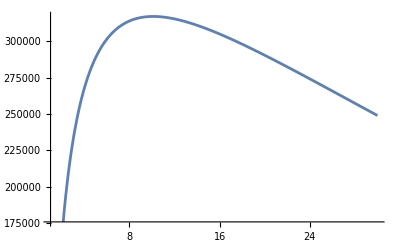

```mathematica
Plot[calcTG[T1,p1,βc,T3,γ,R,ηc,ηe][[1]],{βc,1,30}]
```

## Manipulate Lu(βc,T3)

```mathematica
T1=288;
p1=0.1*10^6;
γ=1.4;
R=287;
ηc=0.8;
ηe=0.9;
```

```mathematica
calcTG[T1,p1,βc,T3,γ,R,ηc,ηe];
```

```mathematica
Manipulate[Plot[calcTG[T1,p1,βc,T3,γ,R,ηc,ηe][[1]],{βc,1,30}],{T3,800,2500}]
```

## Contour Plot ηth(βc,τ)

```mathematica
T1=288;
p1=0.1*10^6;
γ=1.4;
R=287;
ηc=0.8;
ηe=0.9;
```

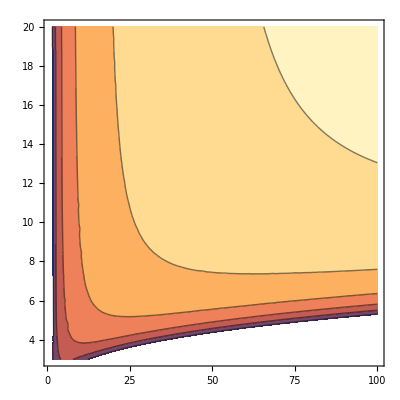

```mathematica
ContourPlot[calcTG[T1,p1,βc,τ T1,γ,R,ηc,ηe][[2]],{βc,1,100},{τ,3,20}]
```

## Grafico T-s

```mathematica
T[s,Tin]:=Tin*Exp[(s-s1)/cp]
```

```mathematica
T1=288;
p1=0.1*10^6;
βc=8;
T3=1500;
γ=1.4;
R=287;
ηc=0.8;
ηe=0.9;
s1=0;

T2s=compressione[T1,p1,βc,γ,R,ηc,s1][[1]]
T2=compressione[T1,p1,βc,γ,R,ηc,s1][[2]]
s2s=compressione[T1,p1,βc,γ,R,ηc,s1][[3]]
s2=compressione[T1,p1,βc,γ,R,ηc,s1][[4]]
```

```mathematica
souts
```

0

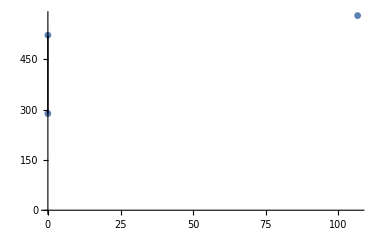

```mathematica
Show[
ListPlot[{{s1,T1},{s2s,T2s},{s2,T2}}],
Graphics[{Line[{{s1,T1},{s2s,T2s}}]},{Line[{s3,T3},{s4s,T4s}]}],
Plot[T[s,T2],{s,s2,s3}],
Plot[T[s,T1],{s,s1,s4}]
]
```

```mathematica
Plot[s1,{T,0,3000}]
```